# SR1 and SMW

The SMW identity gives a cheap way to solve a slightly modified linear system.  The SR1 update formula is a simple way to incorporate a “secant” piece of information into an approximation to a symmetric matrix. We are going to look at both these “little” pieces of linear algebra alone and then incorporate them into a simple optimization algorithm.

### Sherman Morrison Woodbury (SMW)

The lemma says that
	(A+U.C.V)^-1=A^-1-A^-1.U.(C^-1+V.A^-1.U)^-1.V.A^-1
Checking this analytically or numerically is easy.  I am doing numerically basically just to check I have not mistyped anything. It looks like it works.

```mathematica
{m,r}={111,4};
A=RandomReal[{-1,1},{m,m}];
CMat=RandomReal[{-1,1},{r,r}];
U=RandomReal[{-1,1},{m,r}];
V=RandomReal[{-1,1},{r,m}];
InvA=Inverse[A];
SMW=InvA-InvA.U.Inverse[Inverse[CMat]+V.InvA.U].V.InvA;
Norm[Inverse[A+U.CMat.V]-SMW]/Norm[InvA]
```

9.76171×10^-15

So what is it good for?  It is useful if we know some way to compute A^-1 or maybe A^-1.y cheaply and we want to solve (A+U.C.V)z=b.  Quasi-Newton algorithms choose updates to make this useful.

The simplest version (called the Sherman Morrison lemma) is when U is the ultimate tall skinny matrix (a single column) and V is the ultimate short stout matrix (a single row). This gives an expression for the inverse of A+u⊗v. This is the version underlying the standard (non-block) QN optimization algorithms.  Here is a function implementing it.

```mathematica
SM[A_,{u_,v_}]:= Module[{InvA=Inverse[A]},

InvA-InvA.(KroneckerProduct[u,v]/(1+v.InvA.u)).InvA
]
(* Testing *)
m=12;
A=RandomReal[{-1,1},{m,m}];
{u,v}=RandomReal[{-1,1},{2,m}];
Norm[Inverse[A+KroneckerProduct[u,v]]-SM[A,{u,v}]]
```

1.37343×10^-14

### SR1 Updates

The simplest symmetric update of a symmetric matrix B_k to a matrix B_(k+1) satisfying the secant condition
	B_(k+1)s=y
is the SR1 update
	 B_(k+1)=B_k+((y-B_k.s)⊗(y-B_k.s))/((y-B_k.s).s)
it is well defined provided (y-B_k.s).s≠0.  Again it is easy to check analytically or numerically that it works. The following is going to verify that random samples can drive approximations to a given symmetric matrix. First just making an update function and testing that it does what we think it should!

```mathematica
SR1[Bk_,{s_,y_}]:=Module[{z=y-Bk.s,α,Tol=1.0*10^-10},
α=z.s;
If[Abs[α]>Tol, Bk+KroneckerProduct[z,z]/α,Bk]
]
```

```mathematica
(* testing *)
m=12;
{B,Bk}=RandomReal[{-1,1},{2,m,m}];
{B,Bk}={B,Bk}+{Bᵀ,Bkᵀ};
s=RandomReal[{-1,1},m];
y=B.s;
BNew=SR1[Bk,{s,y}];
Norm[y-BNew.s]
```

3.59668×10^-15

This looks good. I am going to pick random directions and correct in those directions to see what happens.  In some sense this should not be surprising! If I correct in enough “independent” directions I will have “hit” all the directions there are!

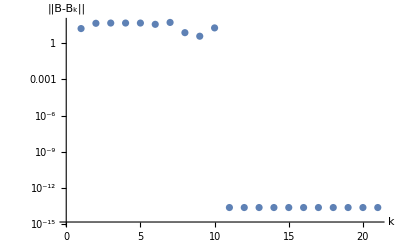

```mathematica
m=11;
{B,Bk}=RandomReal[{-1,1},{2,m,m}];
{B,Bk}={B,Bk}+{Bᵀ,Bkᵀ};
MaxIter=21;
Data=Table[
s=RandomReal[{-1,1},m];
y=B.s;
Bk=SR1[Bk,{s,y}];
Norm[B-Bk],
{MaxIter}
];
ListLogPlot[Data,
AxesLabel->{"k","||B-B_k||"}]
```

## An SR1-SMW Algorithm

I want to approximately minimize f(x) without ever evaluating the second derivative ∇^2 f.  To avoid all sorts of complications I am going to assume that f is strictly convex i.e.
	f(α x+(1-α)y)<α f(x)+(1-α)f(y) for α∈(0,1)
This ensures that there is a single unique minimizer x^*.  I am going to make sure that this is true in an example by adding a scalar multiple of the quadratic term x.x to a small perturbation.

```mathematica
f[x_List]:= 0.5 x.x+0.05*(x[[1]]+2x[[2]])^2+0.05(Sin[x+Reverse[x]]*Sin[RotateLeft[x,1]]-Cos[RotateLeft[x,2]]*Reverse[x]).(Sin[x-Reverse[x]]-Cos[ArcTan[Reverse[x]+x]])
```

We need to be able to compute derivatives! This is our first hint that this could be a major pain in the real world. Here is one way to build a first derivative function df and a second derivative function ddf.

```mathematica
Clear[x,df,ddf]
m=4;
Quiet[vars=Table[x⟦i⟧,{i,m}]];
df[x_]=D[f[vars],{vars}];
ddf[x_]=D[f[vars],{vars,2}];
```

The built in commands work.

```mathematica
x0=RandomReal[{-1,1},m];
FindMinimum[f[x],{x,x0}]
```

{-0.00501033,{x→{-0.0471502,-0.0374766,-0.0573305,-0.0569719}}}

A Newton algorithm consists of approximating the nonlinear vector equation 
	∇f(x_k+u)=0 
with the Taylor series 
	∇f(x_k)+∇^2 f(x_k).u=0 
and updating using
	x_(k+1)=x_k-LinearSolve[∇^2 f(x_k),∇f(x_k)]
since u=-LinearSolve[∇^2 f(x_k),∇f(x_k)]. The simplest algorithm would simply keep fingers and toes crossed that it converges. It does in this case!

```mathematica
MaxIter=6;
xk=x0;
Data=Table[
xk=xk-LinearSolve[ddf[xk],df[xk]],
{MaxIter}];
Quiet[TableForm[Data,TableHeadings->{Automatic,vars}]]
```

| x⟦1⟧ | x⟦2⟧ | x⟦3⟧ | x⟦4⟧
1 | -0.0209507 | -0.115595 | -0.0149952 | -0.0137089
2 | -0.0478273 | -0.0373812 | -0.0573729 | -0.0573026
3 | -0.0471504 | -0.0374766 | -0.0573305 | -0.0569719
4 | -0.0471502 | -0.0374766 | -0.0573305 | -0.0569719
5 | -0.0471502 | -0.0374766 | -0.0573305 | -0.0569719
6 | -0.0471502 | -0.0374766 | -0.0573305 | -0.0569719

If we approximate the second derivative by some matrix B_k we get a secant like algorithm 	
	u=-LinearSolve[B_k,∇f(x_k)]. 
The simplest such algorithm would approximate B_k=I which might converge
 in this case

```mathematica
MaxIter=16;
xk=x0;
Bk=IdentityMatrix[m];
Data=Table[
xk=xk-LinearSolve[Bk,df[xk]],
{MaxIter}];
Quiet[TableForm[Data,TableHeadings->{Automatic,vars}]]
```

| x⟦1⟧ | x⟦2⟧ | x⟦3⟧ | x⟦4⟧
1 | -0.141066 | -0.360245 | 0.0174031 | -0.0121375
2 | 0.0214185 | 0.161391 | -0.100038 | -0.0937076
3 | -0.0898193 | -0.156525 | -0.030896 | -0.026071
4 | -0.0191454 | 0.0376144 | -0.0728471 | -0.0750267
5 | -0.0644544 | -0.0839345 | -0.0474813 | -0.0448689
6 | -0.0361743 | -0.0082608 | -0.0633857 | -0.0643027
7 | -0.0539757 | -0.055693 | -0.0535099 | -0.0522737
8 | -0.042858 | -0.0260508 | -0.0597072 | -0.0598726
9 | -0.0498295 | -0.0446181 | -0.0558377 | -0.05514
10 | -0.0454702 | -0.0330028 | -0.0582627 | -0.0581122
11 | -0.0482006 | -0.0402753 | -0.0567461 | -0.0562556
12 | -0.0464923 | -0.0357242 | -0.0576959 | -0.0574192
13 | -0.0475619 | -0.0385732 | -0.0571016 | -0.0566915
14 | -0.0468925 | -0.0367901 | -0.0574736 | -0.0571472
15 | -0.0473115 | -0.0379063 | -0.0572408 | -0.056862
16 | -0.0470492 | -0.0372076 | -0.0573866 | -0.0570406

Another algorithm might approximate B_1=I (which would not be too bad in this case) and update Bk using the SR1 update.

Yet another algorithm might approximate B_1=I (which would not be too bad in this case), update Bk using the SR1 update, compute H_k=(B_k)^-1 using the SMW formula and simply iterate
	x_(k+1)=x_k-H_k.∇f(x_k)